```mathematica
Clear[N1,tmax,dt,tlist,α,t]
N1=10000;
tmax=30;
dt=0.2;
tlist=Range[0,tmax,dt];
```

```mathematica
tempfile=FileNameJoin[{"/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code","otoc105n1m1.wl"}]
otoc11=Get[tempfile];
tempfile=FileNameJoin[{"/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code","otoc105n1m3.wl"}]
otoc31=Get[tempfile];
tempfile=FileNameJoin[{"/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code","otoc105n3m3.wl"}]
otoc33=Get[tempfile];
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/otoc105n1m1.wl

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/otoc105n1m3.wl

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/otoc105n3m3.wl

```mathematica
fig11=ListPlot[otoc11,PlotRange->All];
fig31=ListPlot[otoc31,PlotRange->All];
fig33=ListPlot[otoc33,PlotRange->All];
```

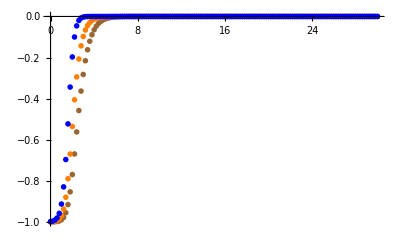

```mathematica
fig=ListPlot[{otoc11,otoc31,otoc33},PlotRange->All,PlotMarkers->"OpenMarkers",PlotStyle->{Brown,Orange,Blue}]
```

```mathematica
ana1[t_]:=-(ⅇ^(-λ t)*N1/8)^(1/2*(m))*HypergeometricU[1/2*(m),1+(m-n)/2,ⅇ^(-λ t)*N1/8]/.{λ->4}
```

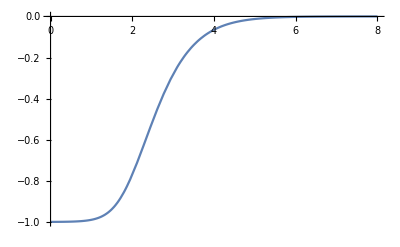

```mathematica
fig11a=Plot[ana1[t]/.{n->1,m->1},{t,0,8},PlotRange->All]
```

```mathematica
fig11a=Plot[ana1[t]/.{n->1,m->1},{t,0,10},PlotRange->All,PlotStyle->{Red},PlotLegends->"one"];
fig31a=Plot[ana1[t]/.{n->1,m->3},{t,0,10},PlotRange->All,PlotLegends->"two"];
fig33a=Plot[ana1[t]/.{n->3,m->3},{t,0,10},PlotRange->All];
```

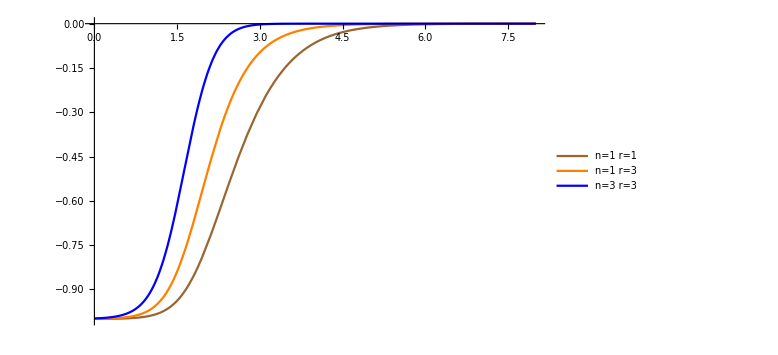

```mathematica
figa=Plot[{ana1[t]/.{n->1,m->1},ana1[t]/.{n->1,m->3},ana1[t]/.{n->3,m->3}},{t,0,8},PlotLegends->Placed[{Style["n=1 r=1",18],Style["n=1 r=3",18], Style["n=3 r=3",18]},{0.9,0.5}],PlotStyle->{Brown,Orange,Blue},ImageSize->Large]
```

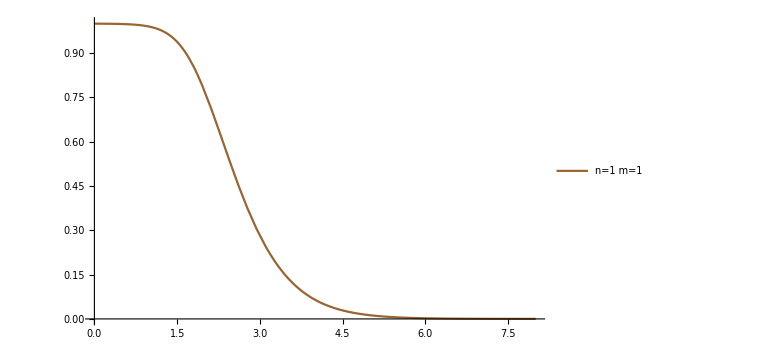

```mathematica
figa=Plot[-ana1[t]/.{n->1,m->1},{t,0,8},PlotLegends->Placed[{Style["n=1 m=1",18]},{0.9,0.5}],PlotStyle->{Brown},ImageSize->Large]
```

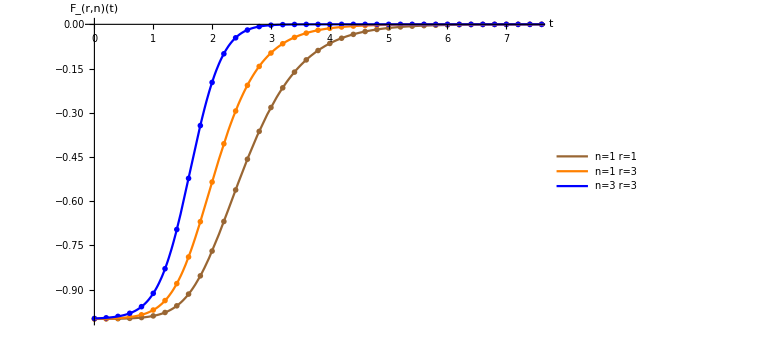

```mathematica
figf=Show[fig,figa,PlotRange->{{0,7.5},All},AxesStyle->16,AxesLabel->{Style[t,20,Black],Style[ToExpression["F_{r,n}(t)",TeXForm,HoldForm],20,Black]
},ImageSize->Large]
```

```mathematica
fig=ListPlot[{otoc11},PlotRange->All,PlotMarkers->"OpenMarkers",PlotStyle->{Brown,Orange,Blue}];
figa=Plot[{ana1[t]/.{n->1,m->1}},{t,0,8},PlotLegends->Placed[{Style["n=1 m=1",18],Style["n=1 m=3",18], Style["n=3 m=3",18]},{0.9,0.5}],PlotStyle->{Brown,Orange,Blue},ImageSize->Large];
figf=Show[fig,figa,PlotRange->{{0,7.5},All},AxesStyle->16,AxesLabel->{Style[t,20,Black],Style[ToExpression["F_{m,n}(t)",TeXForm,HoldForm],20,Black]
},ImageSize->Large]
```

```mathematica
Export["/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf",figf]
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf

```mathematica
Clear[a,t,N1,P,m,s]
```

```mathematica
N1=10000;
a=(N1 ⅇ^(-4 t))/8;
P1[ξ_]:=(4 a^(m/2))/(Gamma[m/2](-ξ)^3)((1-ξ^2)/ξ^2)^(m/2-1)ⅇ^((-a(1-ξ^2))/ξ^2)
P2[s_]:=2*P1[ξ]/.{ξ->2s-1}
```

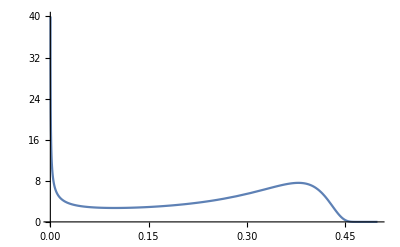

```mathematica
Plot[P2[s]/.{t->2.5,m->1},{s,0,1},PlotRange->{All,{0,40}}]
```

```mathematica
P1[-0.999]/.{m->2}
```

2.00601 ⅇ^(-2.50376 ⅇ^(-4 t))

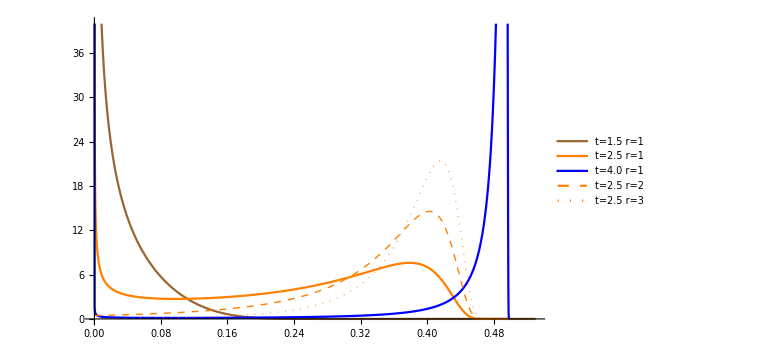

```mathematica
figsize=Plot[{P2[s]/.{t->1.5,m->1},P2[s]/.{t->2.5,m->1},P2[s]/.{t->4,m->1},P2[s]/.{t->2.5,m->2},P2[s]/.{t->2.5,m->3}},{s,0,1},PlotRange->{All,{0,40}},PlotLegends->Placed[{Style["t=1.5 r=1",18],Style["t=2.5 r=1",18], Style["t=4.0 r=1",18],Style["t=2.5 r=2",18],Style["t=2.5 r=3",18]},{0.65,0.8}],PlotStyle->{Brown,Orange,Blue,{Orange,Dashed,Thick},{Orange,Dotted,Thick}},AxesStyle->16,ImageSize->Large]
```

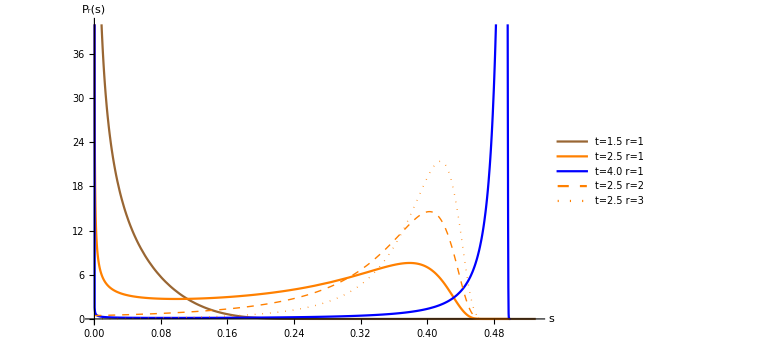

```mathematica
figsizef=Show[figsize,AxesLabel->{Style[s,20,Black],Style[ToExpression["P_r(s)",TeXForm,HoldForm],20,Black]
}]
```

```mathematica
Export["/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf",figsizef]
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf

```mathematica
N1=10000;
star=400;
eqns={-ξ'[t]==2ξ[t](1-ξ[t]^2)+2/N1(-ξ[t]^3-3ξ[t])-6 ϵ[t] ξ[t],ϵ'[t]==4/N1(1-ξ[t]^4)-4ϵ[t] (1-3 ξ[t]^2),ϵ[0]==0,ξ[0]==(2 star)/N1-1};
s=NDSolve[eqns,{ξ,ϵ},{t,-3000,10}]
```

{{ξ→InterpolatingFunction[…],ϵ→InterpolatingFunction[…]}}

```mathematica
figax=Plot[ξ[t]/.s,{t,0,10},PlotRange->All];
figae=Plot[N1*ϵ[t]/.s,{t,0,10},PlotRange->All];
```

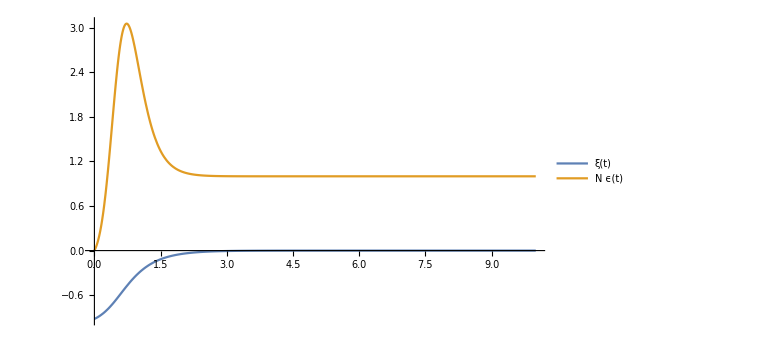

```mathematica
figNsol=Plot[{ξ[t]/.s,N1*ϵ[t]/.s},{t,0,10},PlotRange->All,PlotLegends->Placed[{Style[ToExpression["\\xi(t)",TeXForm,HoldForm],18],Style[ToExpression["N\\epsilon(t)",TeXForm,HoldForm],18]},{0.84,0.8}],AxesStyle->16,ImageSize->Large]
```

```mathematica
Export["/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf",figNsol]
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf

```mathematica
eqns1={-ξ'[t]==2ξ[t](1-ξ[t]^2)+2/N1(-ξ[t]^3-3ξ[t])-6/N1 ξ[t],ξ[0]==(2 star)/N1-1};
s1=DSolve[eqns1,ξ,t]
```

{{ξ→Function[{t},-(23 √9994)/(√(5290529+955721 ⅇ^(4997 t/1250)))]}}

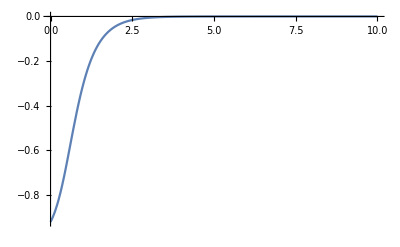

```mathematica
fig2x=Plot[ξ[t]/.s1,{t,0,10},PlotRange->All]
```

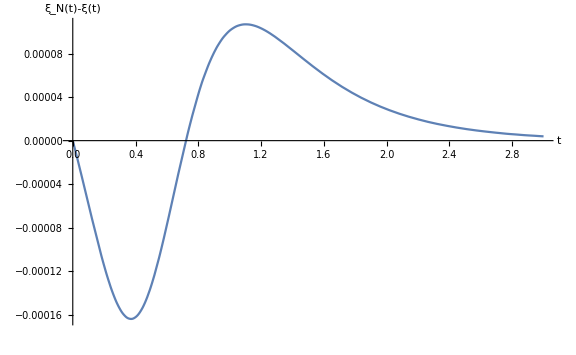

```mathematica
fig31=Plot[((ξ[t]/.s1)-(ξ[t]/.s)),{t,0,3},PlotRange->All,AxesStyle->16,ImageSize->Large,AxesLabel->{Style[t,20,Black],Style[ToExpression["\\xi_{N}(t)-\\xi(t)",TeXForm,HoldForm],20,Black]
}]
```

```mathematica
Export["/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf",fig31]
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf

```mathematica
Clear[N1,tmax,dt,tlist,α,t]
N1=10000;
tmax=1;
dt=0.02;
tlist=Range[0,tmax,dt];
tempfile=FileNameJoin[{"/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code","otoc105n1m1early.wl"}]
otoc11early=Get[tempfile];
ana1[t_]:=-(ⅇ^(-λ t)*N1/8)^(1/2*(m))*HypergeometricU[1/2*(m),1+(m-n)/2,ⅇ^(-λ t)*N1/8]/.{λ->4}
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/otoc105n1m1early.wl

```mathematica
diffearly=ConstantArray[0,{Length[tlist],2}];
Do[diffearly[[temp,2]]=(otoc11early[[temp,2]]-(ana1[otoc11early[[temp,1]]]/.{n->1,m->1}))/((ana1[otoc11early[[temp,1]]]/.{n->1,m->1})*ⅇ^(4*otoc11early[[temp,1]]));diffearly[[temp,1]]=otoc11early[[temp,1]],{temp,1,Length[otoc11early]}]
```

```mathematica
Length[tlist]
```

51

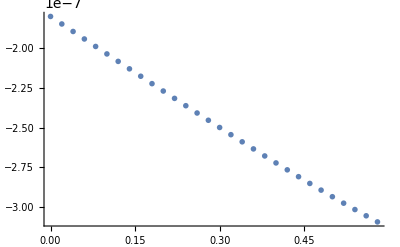

```mathematica
figdiffearly=ListPlot[diffearly[[1;;30]],PlotMarkers->"OpenMarkers"]
```

```mathematica
f1=Fit[diffearly[[1;;25]],{1,x},x]
```

-1.80525×10^-7-2.29757×10^-7 x

```mathematica
N[2.298/0.4]
```

5.745

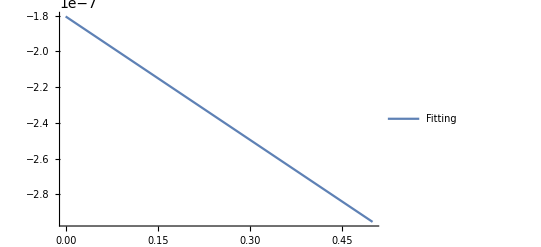

```mathematica
figdiffearly2=Plot[f1,{x,0,0.5},PlotLegends->Placed[{Style[ToExpression["Fitting",TeXForm,HoldForm],18]},{0.84,0.8}]]
```

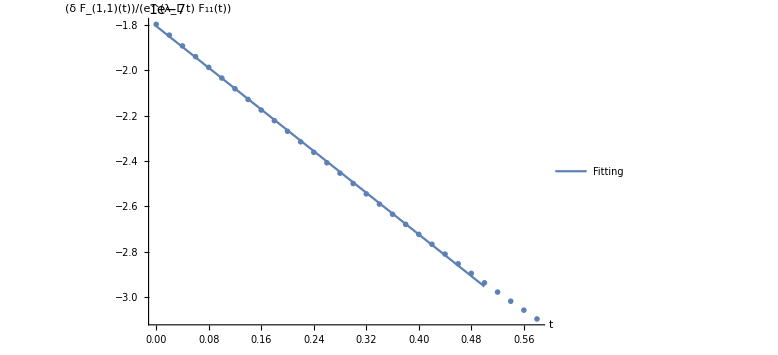

```mathematica
figdiff=Show[figdiffearly,figdiffearly2,AxesStyle->16,ImageSize->Large,AxesLabel->{Style[t,20,Black],Style[ToExpression["\\frac{1}{e^{\\lambda_L t}}\\frac{\\delta F_{1,1}(t)}{F_{11}(t)}",TeXForm,HoldForm],20,Black]
}]
```

```mathematica
Export["/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf",figdiff]
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf

```mathematica
Clear[N1,tmax,dt,tlist,α,t]
N1=10000;
tmax=30;
dt=0.2;
tlist=Range[0,tmax,dt];
tempfile=FileNameJoin[{"/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code","otoc105n1m1.wl"}]
otoc11late=Get[tempfile];
ana1[t_]:=-(ⅇ^(-λ t)*N1/8)^(1/2*(m))*HypergeometricU[1/2*(m),1+(m-n)/2,ⅇ^(-λ t)*N1/8]/.{λ->4}
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/otoc105n1m1.wl

```mathematica
difflate=ConstantArray[0,{Length[tlist],2}];
Do[difflate[[temp,2]]=(otoc11late[[temp,2]]-(ana1[otoc11late[[temp,1]]]/.{n->1,m->1}))/(ana1[otoc11late[[temp,1]]]/.{n->1,m->1});difflate[[temp,1]]=otoc11late[[temp,1]],{temp,1,Length[otoc11late]}]
```

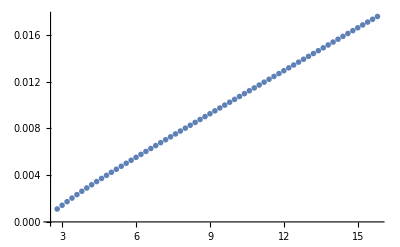

```mathematica
figlate1=ListPlot[difflate[[15;;80]],PlotMarkers->"OpenMarkers"]
```

```mathematica
tlist[[80]]
```

15.8

```mathematica
f2=Fit[difflate[[20;;80]],{1,x},x]
```

-0.00192366+0.00123851 x

```mathematica
N[1.24/0.2]
```

6.2

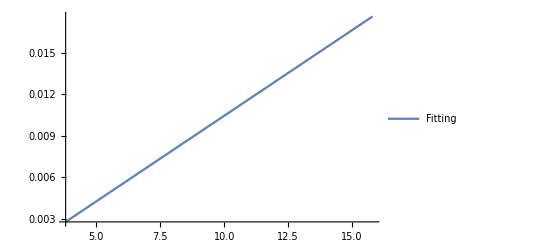

```mathematica
figlate2=Plot[f2,{x,3.8,15.8},PlotLegends->Placed[{Style[ToExpression["Fitting",TeXForm,HoldForm],18]},{0.2,0.8}]]
```

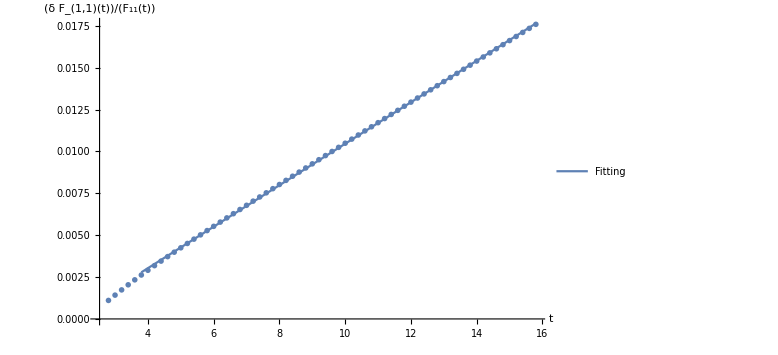

```mathematica
figdifflate=Show[figlate1,figlate2,AxesStyle->16,ImageSize->Large,AxesLabel->{Style[t,20,Black],Style[ToExpression["\\frac{\\delta F_{1,1}(t)}{F_{11}(t)}",TeXForm,HoldForm],20,Black]
}]
```

```mathematica
Export["/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf",figdifflate]
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf

```mathematica
Clear[N1,tmax,dt,tlist,α,t]
N1=10000;
a1=(N1 ⅇ^(-4 t(1-6/N1)))/8;
```

```mathematica
P1N[ξ_]:=(4 a1^(m/2))/(Gamma[m/2](-ξ)^3)((1-ξ^2)/ξ^2)^(m/2-1)ⅇ^((-a1(1-ξ^2))/ξ^2)
```

```mathematica
P1NN[ξ_]:=NIntegrate[√(N1/(2π))*P1N[x]*ⅇ^(-N1/2(ξ-x)^2)/.{m->1,t->3.6},{x,-1,0}]
```

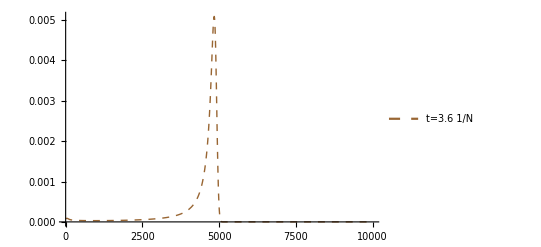

```mathematica
fig2Nsize=Plot[2/N1 P1NN[2/N1*s-1],{s,0,N1},PlotRange->All,PlotStyle->{Dashed,Thick,Brown},PlotLegends->Placed[{Style["t=3.6 1/N",18]},{0.77,0.6}]]
```

```mathematica
Clear[N1]
coef1C[m_]:=((2 m-N1) (2 m+N1) (8+4 m^2-6 N1+N1^2))/(4 N1^3);
coef2C[m_]:=-((4+2 m-N1) (2 m+N1) (2+2 m+N1) (4+2 m+N1))/(8 N1^3);
coef3C[m_]:=-((-4+2 m-N1) (-2+2 m-N1) (2 m-N1) (-4+2 m+N1))/(8 N1^3);
N1=10000;
Emat=ConstantArray[0,{N1+1,N1+1}];
Do[{Emat[[i,i-2]]=coef3C[i-N1/2-1],Emat[[i,i+2]]=coef2C[i-N1/2-1],Emat[[i,i]]=coef1C[i-N1/2-1]},{i,3,N1-1}]
Emat[[2,2]]=coef1C[-N1/2+1];
Emat[[2,4]]=coef2C[-N1/2+1];
Emat[[1,1]]=coef1C[-N1/2];
Emat[[1,3]]=coef2C[-N1/2];
Emat[[N1,N1]]=coef1C[N1/2-1];
Emat[[N1,N1-2]]=coef3C[N1/2-1];
Emat[[N1+1,N1+1]]=coef1C[N1/2];
Emat[[N1+1,N1-1]]=coef3C[N1/2];
Pini=ConstantArray[0,{N1+1,1}];
```

```mathematica
tmax=30;
dt=0.1;
evomat=MatrixExp[Emat*dt];
Pini[[2,1]]=1;
```

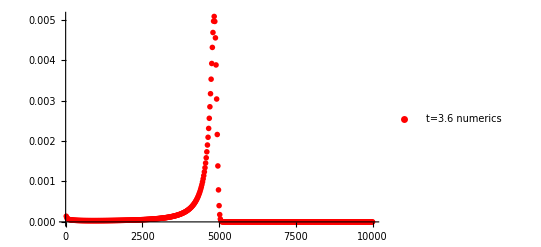

```mathematica
(*pf01=evomat.pf01;*)
pf01plot=Table[{20n,pf01[[20n,1]]},{n,1,N1/20}];
fig1Nsize21=ListPlot[pf01plot,PlotRange->All,PlotMarkers->{"OpenMarkers",Small},PlotStyle->{Red},PlotLegends->Placed[{Style["t=3.6 numerics",18]},{0.77,0.8}]]
```

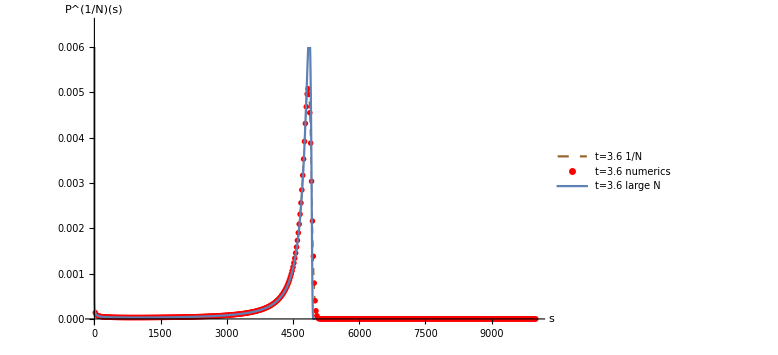

```mathematica
figsizeout=Show[fig2Nsize,fig1Nsize21,fig2size,PlotRange->{All,{0,0.0065}},AxesLabel->{Style[s,20,Black],Style[ToExpression["P^{1/N}(s)",TeXForm,HoldForm],20,Black]
},AxesStyle->16,ImageSize->Large]
```

```mathematica
Export["/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf",figsizeout]
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf

```mathematica
a=(N1 ⅇ^(-4 t))/8;
P1[ξ_]:=(4 a^(m/2))/(Gamma[m/2](-ξ)^3)((1-ξ^2)/ξ^2)^(m/2-1)ⅇ^((-a(1-ξ^2))/ξ^2)
P2[s_]:=2*P1[ξ]/.{ξ->2s-1}
```

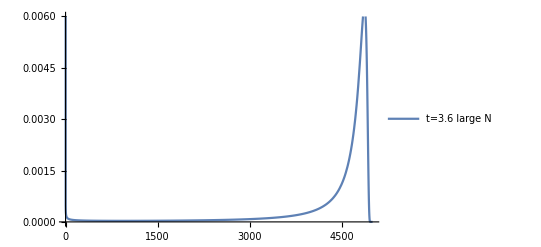

```mathematica
fig2size=Plot[1/N1 P2[s/N1]/.{t->3.6,m->1},{s,0,N1/2},PlotRange->{All,0.006},PlotLegends->Placed[{Style["t=3.6 large N",18]},{0.77,0.7}]]
```

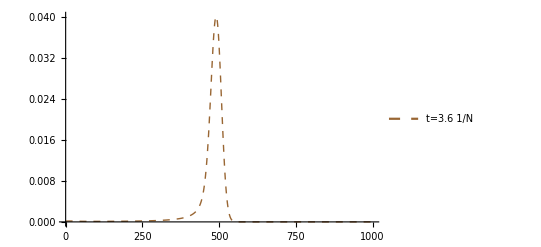

```mathematica
Clear[N1,tmax,dt,tlist,α,t]
N1=1000;
a1=(N1 ⅇ^(-4 t(1-6/N1)))/8;
P1N[ξ_]:=(4 a1^(m/2))/(Gamma[m/2](-ξ)^3)((1-ξ^2)/ξ^2)^(m/2-1)ⅇ^((-a1(1-ξ^2))/ξ^2)
P1NN[ξ_]:=NIntegrate[√(N1/(2π))*P1N[x]*ⅇ^(-N1/2(ξ-x)^2)/.{m->1,t->3.6},{x,-1,0}]
fig2Nsize=Plot[2/N1 P1NN[2/N1*s-1],{s,0,N1},PlotRange->All,PlotStyle->{Dashed,Thick,Brown},PlotLegends->Placed[{Style["t=3.6 1/N",18]},{0.77,0.6}]]
```

```mathematica
Clear[N1]
coef1C[m_]:=((2 m-N1) (2 m+N1) (8+4 m^2-6 N1+N1^2))/(4 N1^3);
coef2C[m_]:=-((4+2 m-N1) (2 m+N1) (2+2 m+N1) (4+2 m+N1))/(8 N1^3);
coef3C[m_]:=-((-4+2 m-N1) (-2+2 m-N1) (2 m-N1) (-4+2 m+N1))/(8 N1^3);
N1=1000;
Emat=ConstantArray[0,{N1+1,N1+1}];
Do[{Emat[[i,i-2]]=coef3C[i-N1/2-1],Emat[[i,i+2]]=coef2C[i-N1/2-1],Emat[[i,i]]=coef1C[i-N1/2-1]},{i,3,N1-1}]
Emat[[2,2]]=coef1C[-N1/2+1];
Emat[[2,4]]=coef2C[-N1/2+1];
Emat[[1,1]]=coef1C[-N1/2];
Emat[[1,3]]=coef2C[-N1/2];
Emat[[N1,N1]]=coef1C[N1/2-1];
Emat[[N1,N1-2]]=coef3C[N1/2-1];
Emat[[N1+1,N1+1]]=coef1C[N1/2];
Emat[[N1+1,N1-1]]=coef3C[N1/2];
Pini=ConstantArray[0,{N1+1,1}];

tmax=30;
dt=0.1;
evomat=MatrixExp[Emat*dt];
Pini[[2,1]]=1;
```

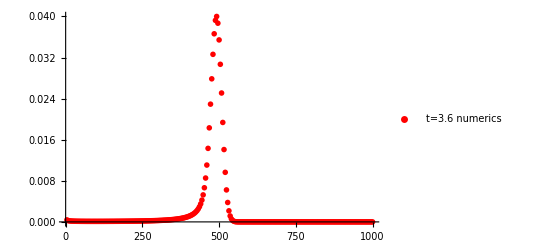

```mathematica
(*pf01=evomat.pf01;*)
pf01=Pini;
Do[pf01=evomat.pf01,{i,1,Round[3.6/dt]}]
pf01plot=Table[{4n,pf01[[4n,1]]},{n,1,N1/4}];
fig1Nsize21=ListPlot[pf01plot,PlotRange->All,PlotMarkers->{"OpenMarkers",Small},PlotStyle->{Red},PlotLegends->Placed[{Style["t=3.6 numerics",18]},{0.77,0.8}]]
```

```mathematica
a=(N1 ⅇ^(-4 t))/8;
P1[ξ_]:=(4 a^(m/2))/(Gamma[m/2](-ξ)^3)((1-ξ^2)/ξ^2)^(m/2-1)ⅇ^((-a(1-ξ^2))/ξ^2)
P2[s_]:=2*P1[ξ]/.{ξ->2s-1}
```

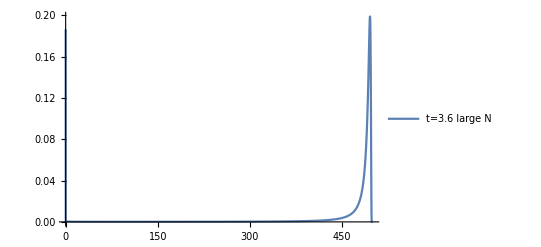

```mathematica
fig2size=Plot[1/N1 P2[s/N1]/.{t->3.6,m->1},{s,0,N1/2},PlotRange->{All,0.2},PlotLegends->Placed[{Style["t=3.6 large N",18]},{0.77,0.7}]]
```

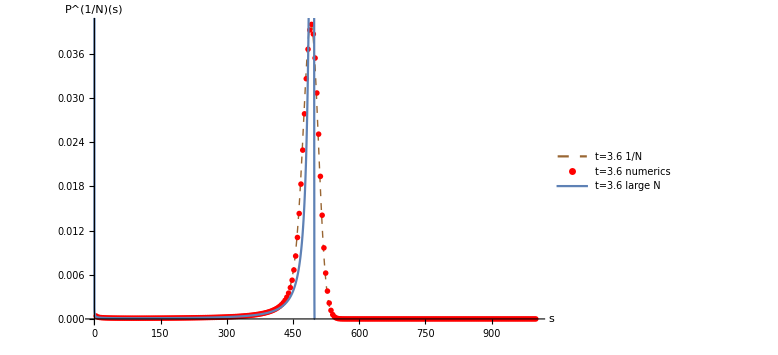

```mathematica
figsizeout=Show[fig2Nsize,fig1Nsize21,fig2size,PlotRange->{All,{0,0.04}},AxesLabel->{Style[s,20,Black],Style[ToExpression["P^{1/N}(s)",TeXForm,HoldForm],20,Black]
},AxesStyle->16,ImageSize->Large]
```

```mathematica
Export["/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf",figsizeout]
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf

```mathematica
Clear[N1]
coef1C[m_]:=((2 m-N1) (2 m+N1) (8+4 m^2-6 N1+N1^2))/(4 N1^3);
coef2C[m_]:=-((4+2 m-N1) (2 m+N1) (2+2 m+N1) (4+2 m+N1))/(8 N1^3);
coef3C[m_]:=-((-4+2 m-N1) (-2+2 m-N1) (2 m-N1) (-4+2 m+N1))/(8 N1^3);
N1=100;
Emat=ConstantArray[0,{N1+1,N1+1}];
Do[{Emat[[i,i-2]]=coef3C[i-N1/2-1],Emat[[i,i+2]]=coef2C[i-N1/2-1],Emat[[i,i]]=coef1C[i-N1/2-1]},{i,3,N1-1}]
Emat[[2,2]]=coef1C[-N1/2+1];
Emat[[2,4]]=coef2C[-N1/2+1];
Emat[[1,1]]=coef1C[-N1/2];
Emat[[1,3]]=coef2C[-N1/2];
Emat[[N1,N1]]=coef1C[N1/2-1];
Emat[[N1,N1-2]]=coef3C[N1/2-1];
Emat[[N1+1,N1+1]]=coef1C[N1/2];
Emat[[N1+1,N1-1]]=coef3C[N1/2];
Pini=ConstantArray[0,{N1+1,1}];

tmax=30;
dt=0.1;
evomat=MatrixExp[Emat*dt];
Pini[[2,1]]=1;
```

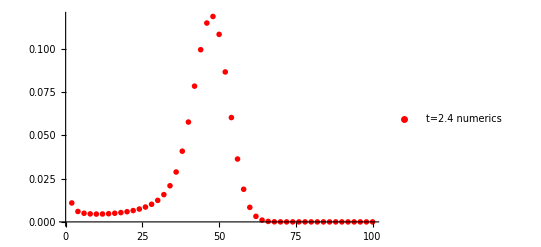

```mathematica
(*pf01=evomat.pf01;*)
pf01=Pini;
Do[pf01=evomat.pf01,{i,1,Round[2.4/dt]}]
pf01plot=Table[{2n,pf01[[2n,1]]},{n,1,N1/2}];
fig1Nsize21=ListPlot[pf01plot,PlotRange->All,PlotMarkers->{"OpenMarkers",Small},PlotStyle->{Red},PlotLegends->Placed[{Style["t=2.4 numerics",18]},{0.77,0.8}]]
```

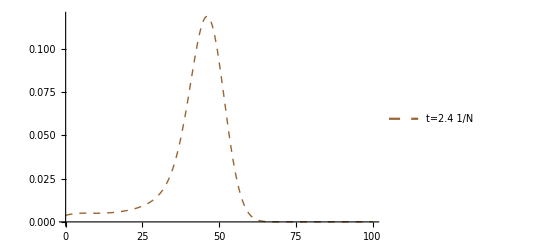

```mathematica
Clear[N1,tmax,dt,tlist,α,t]
N1=100;
a1=(N1 ⅇ^(-4 t(1-6/N1)))/8;
P1N[ξ_]:=(4 a1^(m/2))/(Gamma[m/2](-ξ)^3)((1-ξ^2)/ξ^2)^(m/2-1)ⅇ^((-a1(1-ξ^2))/ξ^2)
P1NN[ξ_]:=NIntegrate[√(N1/(2π))*P1N[x]*ⅇ^(-N1/2(ξ-x)^2)/.{m->1,t->2.4},{x,-1,0}]
fig2Nsize=Plot[2/N1 P1NN[2/N1*s-1],{s,0,N1},PlotRange->All,PlotStyle->{Dashed,Thick,Brown},PlotLegends->Placed[{Style["t=2.4 1/N",18]},{0.77,0.6}]]
```

```mathematica
a=(N1 ⅇ^(-4 t))/8;
P1[ξ_]:=(4 a^(m/2))/(Gamma[m/2](-ξ)^3)((1-ξ^2)/ξ^2)^(m/2-1)ⅇ^((-a(1-ξ^2))/ξ^2)
P2[s_]:=2*P1[ξ]/.{ξ->2s-1}
```

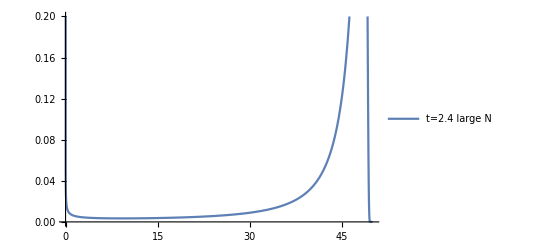

```mathematica
fig2size=Plot[1/N1 P2[s/N1]/.{t->2.4,m->1},{s,0,N1/2},PlotRange->{All,0.2},PlotLegends->Placed[{Style["t=2.4 large N",18]},{0.77,0.7}]]
```

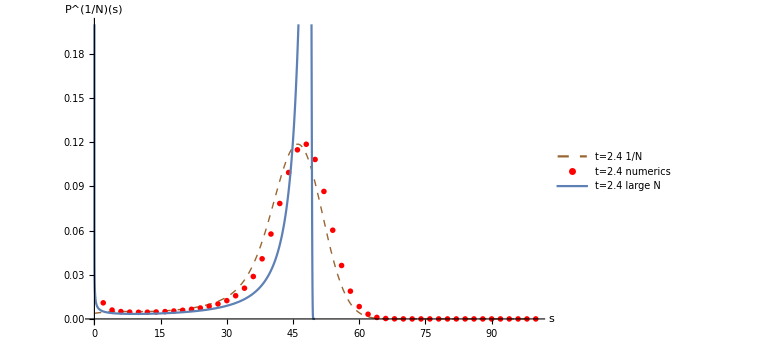

```mathematica
figsizeout=Show[fig2Nsize,fig1Nsize21,fig2size,PlotRange->{All,{0,0.2}},AxesLabel->{Style[s,20,Black],Style[ToExpression["P^{1/N}(s)",TeXForm,HoldForm],20,Black]
},AxesStyle->16,ImageSize->Large]
```

```mathematica
Export["/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf",figsizeout]
```

/Users/shunyuyao/Dropbox/random ideas/wavefront/brownian syk part/code/test2.pdf

```mathematica
Clear[N1]
coef1C[m_]:=((2 m-N1) (2 m+N1) (8+4 m^2-6 N1+N1^2))/(4 N1^3);
coef2C[m_]:=-((4+2 m-N1) (2 m+N1) (2+2 m+N1) (4+2 m+N1))/(8 N1^3);
coef3C[m_]:=-((-4+2 m-N1) (-2+2 m-N1) (2 m-N1) (-4+2 m+N1))/(8 N1^3);
N1=10000;
Emat=ConstantArray[0,{N1+1,N1+1}];
Do[{Emat[[i,i-2]]=coef3C[i-N1/2-1],Emat[[i,i+2]]=coef2C[i-N1/2-1],Emat[[i,i]]=coef1C[i-N1/2-1]},{i,3,N1-1}]
Emat[[2,2]]=coef1C[-N1/2+1];
Emat[[2,4]]=coef2C[-N1/2+1];
Emat[[1,1]]=coef1C[-N1/2];
Emat[[1,3]]=coef2C[-N1/2];
Emat[[N1,N1]]=coef1C[N1/2-1];
Emat[[N1,N1-2]]=coef3C[N1/2-1];
Emat[[N1+1,N1+1]]=coef1C[N1/2];
Emat[[N1+1,N1-1]]=coef3C[N1/2];
Pini=ConstantArray[0,{N1+1,1}];

tmax=30;
dt=0.1;
evomat=MatrixExp[Emat*dt];
Pini[[N1/10,1]]=1;
```

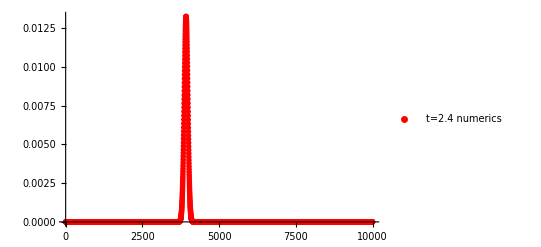

```mathematica
(*pf01=evomat.pf01;*)
pf01=Pini;
Do[pf01=evomat.pf01,{i,1,Round[0.9/dt]}]
pf01plot=Table[{2n,pf01[[2n,1]]},{n,1,N1/2}];
fig1Nsize21=ListPlot[pf01plot,PlotRange->All,PlotMarkers->{"OpenMarkers",Small},PlotStyle->{Red},PlotLegends->Placed[{Style["t=2.4 numerics",18]},{0.77,0.8}]]
```

```mathematica
N1=10000;
star=400;
eqns={-ξ'[t]==2ξ[t](1-ξ[t]^2)+2/N1(-ξ[t]^3-3ξ[t])-6 ϵ[t] ξ[t],ϵ'[t]==4/N1(1-ξ[t]^4)-4ϵ[t] (1-3 ξ[t]^2),ϵ[0]==0,ξ[0]==(2 star)/N1-1};
s=NDSolve[eqns,{ξ,ϵ},{t,-3000,10}]
```

```mathematica
figax=Plot[ξ[t]/.s,{t,0,10},PlotRange->All];
figae=Plot[N1*ϵ[t]/.s,{t,0,10},PlotRange->All];
```

```mathematica
figNsol=Plot[{ξ[t]/.s,N1*ϵ[t]/.s},{t,0,10},PlotRange->All,PlotLegends->Placed[{Style[ToExpression["\\xi(t)",TeXForm,HoldForm],18],Style[ToExpression["N\\epsilon(t)",TeXForm,HoldForm],18]},{0.84,0.8}],AxesStyle->16,ImageSize->Large]
```